# Mini Project 2

## The following project uses graphs to analyze the density of solutions to composite functions of the form f(g(x)) where f(x) = Sin(x).

```mathematica
f=Function[x,Sin[x]];
g1=Function[x,Exp[x]];
f[g1[x]]==0
```

Sin[ⅇ^x]==0

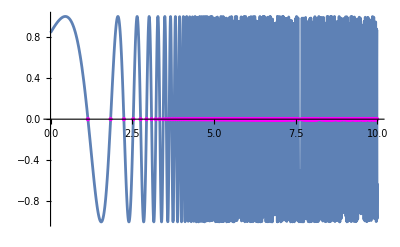

```mathematica
Plot[f[g1[x]],
{x,0,10},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

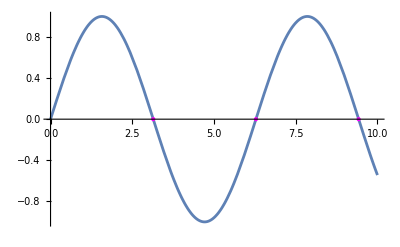

```mathematica
Plot[f[x],
{x,0,10},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

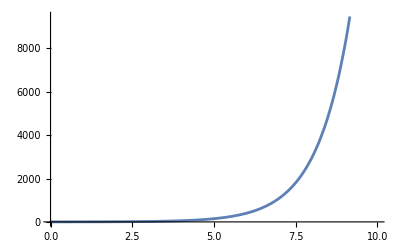

```mathematica
Plot[g1[x],
{x,0,10},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

From the first graph, we notice that the density of solutions increases exponentially as x increases. Looking at the second graph of f(x), the function is periodic and the density of solutions is constant everywhere. Looking at the third graph of g1(x), we see that the inner function g1(x) is increasing at a faster and faster rate as x increases. Therefore, the density of solutions of f(g(x)) is based on the rate of change of the inner function. The faster the inner function is growing in Sin[g1(x)], the greater the density of solutions. Since g1(x) grows really fast as x increases, the density of f(x) will increase really fast as x increases.  Since f(x) is periodic, it is also possible to compute all the solutions as a set, ln[arcsin(0)].  However, it is impossible to graph all the solutions as there are infinite solutions to f(x) = 0 and therefore infinite solutions to f(g1(x)) = 0

```mathematica
g2=Function[x,1/x^2];
f[g2[x]]==0
```

Sin[1/x^2]==0

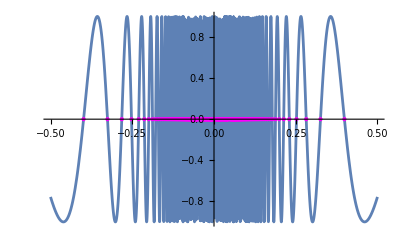

```mathematica
Plot[f[g2[x]],
{x,-0.5,0.5},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

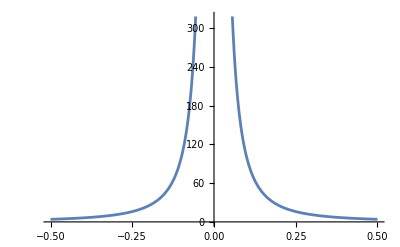

```mathematica
Plot[g2[x],
{x,-0.5,0.5},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

As pointed out in the previous example, the density of solutions for Sin(g2(x)) is dependent on the inner function g2(x). More specifically, the faster g2(x) increases (its rate of change), the higher the density of solutions will be around that point. For g2(x), there is a vertical asymptote at x = 0 as shown in the graph above. Therefore, the density of solutions increases near x = 0 because g2(x) increases at a faster and faster rate as x approaches 0. Since f(x) is periodic, it is possible to compute all the solutions as a set, Sqrt[1/arcsin(0)]. However, it is impossible to graph all the solutions to f(g2(x)) = 0 because there are infinite solutions to f(x) = 0 and therefore infinite solutions to f(g2(x)) = 0.

In order to solve for these solutions, one would first solve f(u) = k to find the values that need to be plugged into f. Then set g(x) = u for all u to find the values x that would satisfy both equations.